# Projekt za ROM

Analiza podatkov o presaditvi organov po svetu.

## Podatki, ki jih bomo uporavljali

```mathematica
podatki=ResourceData["Organ Transplants by Country"]
```

Dataset[<>]

## Analiza Slovenije

Podatki za Slovenijo :

```mathematica
Select[podatki, #["Country"] == LinguisticAssistant&]
```

```mathematica
PresaditevLedvic=%[[1]]["TotalKidneyTransplant"]
```

TimeSeries[…]

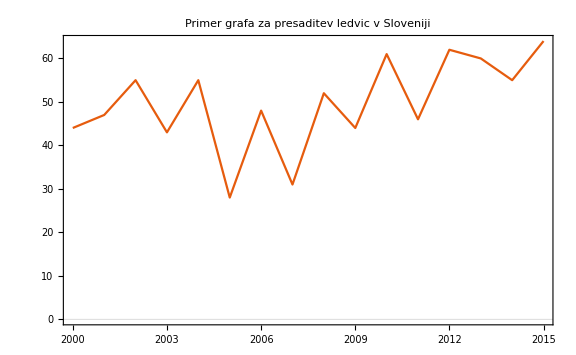

```mathematica
DateListPlot[PresaditevLedvic, PlotLabel->"Primer grafa za presaditev ledvic v Sloveniji ", PlotTheme->"Scientific", ImageSize->Large]
```

## Analiza ostalih držav

Presaditev ledvic na milijon prebivalcev po državah leta 2015:

```mathematica
With[{kidney=podatki[All,{"Country","Population","TotalKidneyTransplant"}]},GeoRegionValuePlot[#[[1]]->(#[[3]]/#[[2]])["LastValue"]&/@Normal[kidney]]]
```

-Graphics-

Presaditev jetr po svetu

```mathematica
With[{jetra=podatki[All,{"Country","Population","TotalHeartTransplant"}]},GeoRegionValuePlot[#[[1]]->(#[[3]]/#[[2]])["LastValue"]&/@Normal[jetra]]]
```

-Graphics-

### Presaditev src v evropski uniji

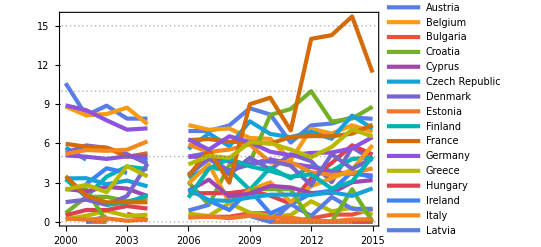

```mathematica
With[{eu=EntityList[LinguisticAssistant],data=podatki},DateListPlot[Legended[#[[3]]/#[[2]],#[[1]]]&/@Normal@data[Select[MemberQ[eu,#Country]&]][[All,{"Country","Population","TotalHeartTransplant"}]],PlotTheme->"Business"]]
```

## Obrazec

Primer obrazca za prikaz grafov o presaditvah ledvic za posamezno državo.

```mathematica
obrazecPodatki[drzava_]:=Module[{vsipodatki,presaditevLedvic},
vsipodatki=ResourceData["Organ Transplants by Country"];
presaditevLedvic=Select[vsipodatki,#["Country"]==drzava&][[1]][["TotalKidneyTransplant"]];
DateListPlot[presaditevLedvic, PlotLabel->StringForm["Prikaz presaditve ledvic po letih za drzavo `` . ", ToUpperCase[drzava["Name"]]],PlotTheme->"Scientific", ImageSize->Large]

]
```

```mathematica
obrazecPodatki[ LinguisticAssistant];
```

```mathematica
obrazec = FormPage["drzava" -> "Country", obrazecPodatki[#drzava] &,AppearanceRules-><|"Title" -> "Presaditve ledvic", "Description" -> "Vnesi ime drzave, za katero zelis prikaz presaditev ledvic od leta 2000 do leta 2015.", "SubmitLabel" -> "Prikazi"|>]
```

```mathematica
CloudDeploy[obrazec,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/b1b7d46a-bce1-4f6d-b0e0-c13d6620f1e8]